# ProjectEuler.net

## Problem 1

If we list all the natural numbers below 10 that are multiples of 3 or 5, we get 3, 5, 6 and 9. The sum of these multiples is 23.

Find the sum of all the multiples of 3 or 5 below 1000.

### Solution 1

#### Algorithm

Create set of all multiples of 3 in the range [3, 1000).
Create set of all multiples of 5 in the range [5, 1000).
Find union of the two sets.
Find sum of the union.

This solution consumes too much memory.

#### Implementation

```mathematica
createMultiplesSet[increment_, upperLimit_]:=Range[increment, upperLimit - 1, increment];
findSolution[upperLimit_] := (
multiplesOf3 = createMultiplesSet [3, upperLimit];
multiplesOf5 = createMultiplesSet [5, upperLimit];
union = Union[multiplesOf3, multiplesOf5];
Clear[multiplesOf3, multiplesOf5];
Total[union]
)
```

```mathematica
findSolution[10]
```

23

```mathematica
AbsoluteTiming[findSolution[1000]]
```

{0.,233168}

```mathematica
AbsoluteTiming[findSolution[10^7]]
```

{1.21507,23333331666668}

```mathematica
Clear[createMultiplesSet, findSolution, union]
```

### Solution 2

#### Algorithm

s3 = sum of the arithmetic progression a = 3, d = 3, n = Floor((1000 - 1) / 3).
s5 = sum of the arithmetic progression a = 5, d = 5, n = Floor((1000 - 1) / 5).
lcm = LCM of 3 and 5 = 15
sLCM = sum of the arithmetic progression a = lcm, d = lcm, n = Floor((1000 - 1) / lcm).
Result = s3 + s5 - sLCM

This is the fastest solution.

#### Implementation

```mathematica
sumArithmeticProgression[increment_, upperLimit_]:=Module[{a, d, n},(
a = d = increment;
n = Floor[(upperLimit - 1)/increment];
n(2a+(n-1)d)/2
)];
findSolution[upperLimit_]:=Module[{s3, s5, lcm, sLCM}, (
s3 = sumArithmeticProgression[3, upperLimit];
s5 = sumArithmeticProgression[5, upperLimit];
lcm = LCM[3, 5];
sLCM = sumArithmeticProgression[lcm, upperLimit];
s3 + s5 - sLCM
)];
```

```mathematica
findSolution[10]
```

23

```mathematica
AbsoluteTiming[findSolution[1000]]
```

{0.,233168}

```mathematica
AbsoluteTiming[findSolution[10^7]]
```

{0.,23333331666668}

```mathematica
Clear[sumArithmeticProgression, findSolution]
```

### Solution 3

#### Algorithm

sum = 0
for each i = 0 → 1000 - 1
	if (i % 3 == 0 || i % 5 == 0)
		sum += i
		
This is the slowest solution.

#### Implementation

```mathematica
findSolution[upperLimit_]:=Module[{sum}, (
sum = 0;
Do[If[Divisible[i, 5]|| Divisible[i, 3], sum+= i], {i, upperLimit - 1}];
sum
)];
```

```mathematica
findSolution[10]
```

23

```mathematica
AbsoluteTiming[findSolution[1000]]
```

{0.002,233168}

```mathematica
AbsoluteTiming[findSolution[10^7]]
```

{29.7247,23333331666668}

```mathematica
Clear[findSolution]
```

## Problem 2

Each new term in the Fibonacci sequence is generated by adding the previous two terms. By starting with 1 and 2, the first 10 terms will be:

1, 2, 3, 5, 8, 13, 21, 34, 55, 89, ...

By considering the terms in the Fibonacci sequence whose values do not exceed four million, find the sum of the even-valued terms.

### Solution 1

#### Thoughts

```mathematica
f[i] = f[i - 1] + f[i - 2]

f1
f2

1 f1 + 1 f2, 1 f1 + 1 f2
1 f1 + 2 f2
2 f1 + 3 f2
3 f1 + 5 f2, 4 f1 + 6 f2
5 f1 + 8 f2
8 f1 + 13 f2
13 f1 + 21 f2, 17 f1 + 27 f2

f[i] = f1 f[i - 2] + f2 f[i - 3]
```

```mathematica
(* Every 3^rd number of the Fibonacci series is even. *)
indices = Range[3, 36, 3];
values = Fibonacci /@ indices;
sums=Accumulate[values];
Grid[Transpose[{indices, values, sums}], Frame->All]
```

3 | 2 | 2
6 | 8 | 10
9 | 34 | 44
12 | 144 | 188
15 | 610 | 798
18 | 2584 | 3382
21 | 10946 | 14328
24 | 46368 | 60696
27 | 196418 | 257114
30 | 832040 | 1089154
33 | 3524578 | 4613732
36 | 14930352 | 19544084

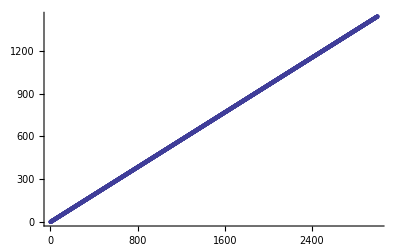

```mathematica
(* Try to define Fibonacci[x] as a function of x without having to evaluate preceding terms. *)
data = Log /@ Fibonacci /@ Range[3000];
fit = Fit[data, {1, x}, x];
Show[ListPlot[data], Plot[fit, {x, 3, 3000}]]
```

```mathematica
fit (* 30 *)
```

-0.776836+0.479852 x

```mathematica
fit (* 100 *)
```

-0.796489+0.481089 x

```mathematica
fit (* 200 *)
```

-0.800618+0.481181 x

```mathematica
fit (* 300 *)
```

-0.801988+0.481198 x

```mathematica
fit (* 3000 *)
```

-0.804446+0.481212 x

```mathematica
E^(fit /.x->7)
```

12.9881

```mathematica
Clear[indices, values, sums, logs, data, fit, f]
```

```mathematica
"3 2" 2^1
"6 8" 2^3
"9 34" 2^5+2^1
"12 144" 2^7+2^4
"15 610" 2^9+2^7
"18 2584"
```

```mathematica
f[x_] :=(GoldenRatio^x-(-GoldenRatio)^(-x))/Sqrt[5]
```

```mathematica
N[f[21]]
```

10946.

#### Algorithm

```mathematica
a = 1;
b = 2;
sum = 0;

while (1)
	fibonacci = a + b;

	if (fibonacci > 4 * 10^6)
		return sum;

	if (fibonacci % 2 == 0)
		sum += fibonacci;

	a = b;
	b = fibonacci;
```

#### Implementation

```mathematica
findSolution[upperLimit_]:= Module[{a, b, sum, fibonacci},(
a = 1;
b = 2;
sum = b;

While[True,
fibonacci = a + b;

If [fibonacci > upperLimit, Return[sum]];

If[EvenQ[fibonacci], sum += fibonacci];

a = b;
b = fibonacci;
]
)]
```

```mathematica
findSolution[4×10^6]
```

4613732

```mathematica
AbsoluteTiming[findSolution[4×10^50]]
```

{0.001,356005627784909427961628962100248171903816414875122}

```mathematica
Clear[findSolution]
```

### Solution 2

#### Algorithm

```mathematica
sum = 0;

for (i = 3; (fibonacci = Fibonacci[i]) <= 4 * 10^6; i += 3)
	sum += fibonacci;

return sum;
```

#### Implementation

```mathematica
findSolution[upperLimit_]:=Module[{sum, fibonacci}, (
sum = 0;

For[i = 3, (fibonacci = Fibonacci[i]) <= upperLimit, i += 3,
sum += fibonacci;
];

Return[sum];
)]
```

```mathematica
findSolution[4×10^6]
```

4613732

```mathematica
AbsoluteTiming[findSolution[4×10^50]]
```

{0.001,356005627784909427961628962100248171903816414875122}

```mathematica
Clear[findSolution]
```

### Solution 3

#### Algorithm

```mathematica
fib[n] = Floor[phi^n/(√5) + 1/2]
Subscript[F, n] < phi^n/(√5) + 1/2
phi^n > √5(Subscript[F, n] - 1/2)
n[Subscript[F, n]] > Log[√5(Subscript[F, n] - 1/2)]/Log[phi]
n[Subscript[F, n]] = Ceiling[Log[√5(Subscript[F, n] - 1/2)]/Log[phi]]

sum = 0
last = 1
nMax = n[upperLimit]

for i = 3 -> nMax; di = 3
	sum += (last = Round[last phi^3])
```

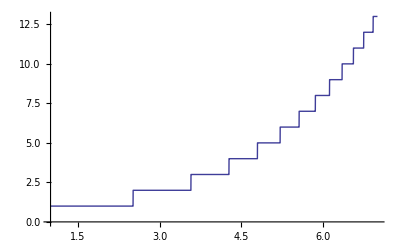

```mathematica
phi = GoldenRatio;
Plot[{y = Floor[phi^n/(√5) + 1/2]},{n,1,7},]
```

#### Implementation

## Problem 3

The prime factors of 13195 are 5, 7, 13 and 29.

What is the largest prime factor of the number 600851475143 ?

WolframAlphaQueryResults

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223}

```mathematica
p = {2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223}
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223}

```mathematica
Grid[Transpose[p, Differences[p]]]
```

Transpose::tperm: Permutation {1, 2, 2, 4, 2, 4, 2, 4, 6, 2, 6, 4, 2, 4, 6, 6, 2, 6, 4, 2, 6, 4, 6, 8, 4, 2, 4, 2, 4, 14, 4, 6, 2, 10, 2, 6, 6, 4, 6, 6, 2, 10, 2, 4, 2, 12, 12, 4, 2, 4, « 149 »} is longer than the dimensions {200} of the array.

Grid[Transpose[{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223},{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6,10,6,6,2,6,10,6,6,2,6,6,4,2,12,10,2,4,6,6,2,12,4,6,8,10,8,10,8,6,6,4,8,6,4,8,4,14,10,12,2,10,2,4,2,10,14,4,2,4,14,4,2,4,20,4,8,10,8,4,6,6,14,4,6,6,8,6,12,4,6,2,10,2,6,10,2,10,2,6,18,4,2,4,6,6,8,6,6,22,2,10,8,10,6,6,8,12,4,6}]]

```mathematica
d = Differences[p]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6,10,6,6,2,6,10,6,6,2,6,6,4,2,12,10,2,4,6,6,2,12,4,6,8,10,8,10,8,6,6,4,8,6,4,8,4,14,10,12,2,10,2,4,2,10,14,4,2,4,14,4,2,4,20,4,8,10,8,4,6,6,14,4,6,6,8,6,12,4,6,2,10,2,6,10,2,10,2,6,18,4,2,4,6,6,8,6,6,22,2,10,8,10,6,6,8,12,4,6}

```mathematica
Length[p]
```

200

```mathematica
Length[d]
```

199

```mathematica
d[0]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6,10,6,6,2,6,10,6,6,2,6,6,4,2,12,10,2,4,6,6,2,12,4,6,8,10,8,10,8,6,6,4,8,6,4,8,4,14,10,12,2,10,2,4,2,10,14,4,2,4,14,4,2,4,20,4,8,10,8,4,6,6,14,4,6,6,8,6,12,4,6,2,10,2,6,10,2,10,2,6,18,4,2,4,6,6,8,6,6,22,2,10,8,10,6,6,8,12,4,6}[0]